```mathematica
(*Import data from the .csv*)
```

```mathematica
s=Import["C:\\Users\\User\\Desktop\\data02.csv"];
```

```mathematica
(*Read data: Measured magnetic field (mBx,mBy,mBz) and orbital data*)
```

```mathematica
Do[mBx[i]=s[[i,1]],{i,1,4871}]
```

```mathematica
Do[mBy[i]=s[[i,2]],{i,1,4871}]
```

```mathematica
Do[mBz[i]=s[[i,3]],{i,1,4871}]
```

```mathematica
Do[lat[i]=s[[i,4]]*Pi/180,{i,1,4871}](*rad*)
```

```mathematica
Do[lon[i]=s[[i,5]]*Pi/180,{i,1,4871}](*rad*)
```

```mathematica
Do[alt[i]=s[[i,6]],{i,1,4871}](*m*)
```

```mathematica
(*Calculate distance to center of Earth (r)*)
```

```mathematica
a=6378137;
```

```mathematica
b=6356752.314245;
```

```mathematica
Do[r[i]=a^2/Sqrt[a^2*Cos[lat[i]]^2+b^2*Sin[lat[i]]^2] + alt[i] ,{i,1,4871}]
```

```mathematica
(*Calculate position in ECEF reference frame: X- Towards 0°N 0°E, Y- Towards 0°N 90°E, Z- Towards North*)
```

```mathematica
posx[r_,lat_,lon_]:=r*Cos[lat]*Cos[lon]
```

```mathematica
posy[r_,lat_,lon_]:=r*Cos[lat]*Sin[lon]
```

```mathematica
posz[r_,lat_,lon_]:=r*Sin[lat]
```

```mathematica
Do[x[i]=posx[r[i],lat[i],lon[i]],{i,1,4871}]
```

```mathematica
Do[y[i]=posy[r[i],lat[i],lon[i]],{i,1,4871}]
```

```mathematica
Do[z[i]=posz[r[i],lat[i],lon[i]],{i,1,4871}]
```

```mathematica
(*Earth radius (for multipole model) and expansion order (n)*)
```

```mathematica
er=6371200;
```

```mathematica
n=3
```

3

```mathematica
(*Defining arrays for the equations*)
```

```mathematica
gl= Table[Table[Subscript[g, j,i],{j,0,i}],{i,1,n}]
```

{{g_(0,1),g_(1,1)},{g_(0,2),g_(1,2),g_(2,2)},{g_(0,3),g_(1,3),g_(2,3),g_(3,3)}}

```mathematica
hl= Table[Table[Subscript[h, j,i],{j,0,i}],{i,1,n}]
```

{{h_(0,1),h_(1,1)},{h_(0,2),h_(1,2),h_(2,2)},{h_(0,3),h_(1,3),h_(2,3),h_(3,3)}}

```mathematica
(*Subscript[h, 0,x] parameters are not used, but they are kept in for symmetry*)
```

```mathematica
(*Calculate magnetic field (in ECEF frame)*)
```

```mathematica
V[r_,lat_,lon_]:=er*Sum[(er/r)^(i+1)*(gl[[i,j]]*Cos[(j-1)*lon]+hl[[i,j]]*Sin[(j-1)*lon])*LegendreP[i,j-1,Sin[lat]]*(-1)^(j-1)*Sqrt[(2-KroneckerDelta[j,1])*(i-j+1)!/(i+j-1)!],{i,1,n},{j,1,i+1}]
```

```mathematica
dvr[r_,lat_,lon_]:=D[V[x,lat,lon],x]/.x->r
```

```mathematica
dvlat[r_,lat_,lon_]:=D[V[r,x,lon],x]/r/.x->lat
```

```mathematica
dvlon[r_,lat_,lon_]:=D[V[r,lat,x],x]/(r*Cos[lat])/.x->lon
```

```mathematica
(*B measures field for any location, while eB is specifically for the ISS's positions*)
```

```mathematica
Bx[r_,lat_,lon_]:=(-Cos[lat]*dvr[r,lat,lon]+Sin[lat]*dvlat[r,lat,lon])*Cos[lon]+Sin[lon]*dvlon[r,lat,lon]
```

```mathematica
By[r_,lat_,lon_]:=(-Cos[lat]*dvr[r,lat,lon]+Sin[lat]*dvlat[r,lat,lon])*Sin[lon]-Cos[lon]*dvlon[r,lat,lon]
```

```mathematica
Bz[r_,lat_,lon_]:=-Sin[lat]*dvr[r,lat,lon]-Cos[lat]*dvlat[r,lat,lon]
```

```mathematica
eBx[i_]:=Bx[r[i],lat[i],lon[i]]
```

```mathematica
eBy[i_]:=By[r[i],lat[i],lon[i]]
```

```mathematica
eBz[i_]:=Bz[r[i],lat[i],lon[i]]
```

```mathematica
(*Field in ISS's reference frame*)
```

```mathematica
iBx[i_]:=((x[i]*x[i-1]+y[i]*y[i-1]+z[i]*z[i-1])*(eBx[i]*x[i]+eBy[i]*y[i]+eBz[i]*z[i])-(x[i]^2+y[i]^2+z[i]^2)*(eBx[i]*x[i-1]+eBy[i]*y[i-1]+eBz[i]*z[i-1]))/Sqrt[x[i]^2+y[i]^2+z[i]^2]/Sqrt[(y[i]*z[i-1]-z[i]*y[i-1])^2+(z[i]*x[i-1]-x[i]*z[i-1])^2+(x[i]*y[i-1]-y[i]*x[i-1])^2]
```

```mathematica
iBy[i_]:=(eBx[i]*x[i]+eBy[i]*y[i]+eBz[i]*z[i])/Sqrt[x[i]^2+y[i]^2+z[i]^2]
```

```mathematica
iBz[i_]:=(eBx[i]*(y[i]*z[i-1]-z[i]*y[i-1])+eBy[i]*(z[i]*x[i-1]-x[i]*z[i-1])+eBz[i]*(x[i]*y[i-1]-y[i]*x[i-1]))/Sqrt[(y[i]*z[i-1]-z[i]*y[i-1])^2+(z[i]*x[i-1]-x[i]*z[i-1])^2+(x[i]*y[i-1]-y[i]*x[i-1])^2]
```

```mathematica
(*Field in RaspberryPi's reference frame*)
```

```mathematica
rBx[al_,be_,ga_,i_]:=Cos[al]*Cos[be]*iBx[i]+(Cos[al]*Sin[be]*Sin[ga]-Sin[al]*Cos[ga])*iBy[i]+(Cos[al]*Sin[be]*Cos[ga]+Sin[al]*Sin[ga])*iBz[i]
```

```mathematica
rBy[al_,be_,ga_,i_]:=Sin[al]*Cos[be]*iBx[i]+(Sin[al]*Sin[be]*Sin[ga]+Cos[al]*Cos[ga])*iBy[i]+(Sin[al]*Sin[be]*Cos[ga]-Cos[al]*Sin[ga])*iBz[i]
```

```mathematica
rBz[al_,be_,ga_,i_]:=-Sin[be]*iBx[i]+Cos[be]*Sin[ga]*iBy[i]+Cos[be]*Cos[ga]*iBz[i]
```

```mathematica
(*Sum of squares of differences, which will be minimized to find the best fit*)
```

```mathematica
sq[al_,be_,ga_]:=Sum[(rBx[al,be,ga,i]-mBx[i])^2+(rBy[al,be,ga,i]-mBy[i])^2+(rBz[al,be,ga,i]-mBz[i])^2,{i,2,4871}]
```

```mathematica
NMinimize[sq[al,be,ga],{al,be,ga,gl[[1,1]],gl[[1,2]],gl[[2,1]],gl[[2,2]],gl[[2,3]],gl[[3,1]],gl[[3,2]],gl[[3,3]],gl[[3,4]],hl[[1,2]],hl[[2,2]],hl[[2,3]],hl[[3,2]],hl[[3,3]],hl[[3,4]]}]
```

{324343.,{al→2.32958,be→0.789503,ga→2.83688,g_(0,1)→-56.0633,g_(1,1)→0.14063,g_(0,2)→-13.3966,g_(1,2)→6.08428,g_(2,2)→4.31868,g_(0,3)→11.0515,g_(1,3)→1.45643,g_(2,3)→18.1936,g_(3,3)→-0.726947,h_(1,1)→61.433,h_(1,2)→12.8321,h_(2,2)→-6.19656,h_(1,3)→2.2583,h_(2,3)→-3.88701,h_(3,3)→-15.3229}}

```mathematica
(*Found parameters*)
```

```mathematica
gl={{-56.063262378488645,0.14062992651524717},{-13.396630570456654,6.084279428556939,4.318684818414627},{11.051469655258256,1.4564283262153426,18.193648193676726,-0.7269466760235817}}
```

{{-56.0633,0.14063},{-13.3966,6.08428,4.31868},{11.0515,1.45643,18.1936,-0.726947}}

```mathematica
hl={{0,61.43295350802794},{0,12.832088289024783,-6.196563485904224},{0,2.2583027476691253,-3.8870120364609098,-15.322853713482681}}
```

{{0,61.433},{0,12.8321,-6.19656},{0,2.2583,-3.88701,-15.3229}}

```mathematica
(*Error percentage function*)
```

```mathematica
al=2.329580898033588
```

2.32958

```mathematica
be=0.789503217886924
```

0.789503

```mathematica
ga=2.8368756025341004
```

2.83688

```mathematica
Error= Sum[Norm[{rBx[al,be,ga,i],rBy[al,be,ga,i],rBz[al,be,ga,i]}-{mBx[i],mBy[i],mBz[i]}],{i,2,4871}]/ Sum[Norm[{mBx[i],mBy[i],mBz[i]}],{i,2,4871}]*100
```

14.8343

```mathematica
(*Calculate North magnetic pole: where the position vector and magnetic field vector are aligned*)
```

```mathematica
NMinimize[{VectorAngle[{posx[er,lat,lon],posy[er,lat,lon],posz[er,lat,lon]},{Bx[er,lat,lon],By[er,lat,lon],Bz[er,lat,lon]}],lat<=Pi/2,lat>=-Pi/2,lon<=Pi, lon>=-Pi},{lat,lon},Method->"RandomSearch"]
```

{0.,{lat→-0.466123,lon→1.608}}

```mathematica
(*26.71S, 92.13E - Indic Ocean, Left of Australia*)
```

```mathematica
(*Calculate South magnetic pole: where the position vector and magnetic field vector are exactly opposite*)
```

```mathematica
NMaximize[{VectorAngle[{posx[er,lat,lon],posy[er,lat,lon],posz[er,lat,lon]},{Bx[er,lat,lon],By[er,lat,lon],Bz[er,lat,lon]}],lat<=Pi/2,lat>=-Pi/2,lon<=Pi, lon>=-Pi},{lat,lon},Method->"RandomSearch"]
```

{3.14159,{lat→0.674399,lon→-1.67855}}

```mathematica
(*38.64N, 96.17W - Kansas, USA *)
```

```mathematica
(*Plot of calculated magnetic field intensity, in μT*)
```

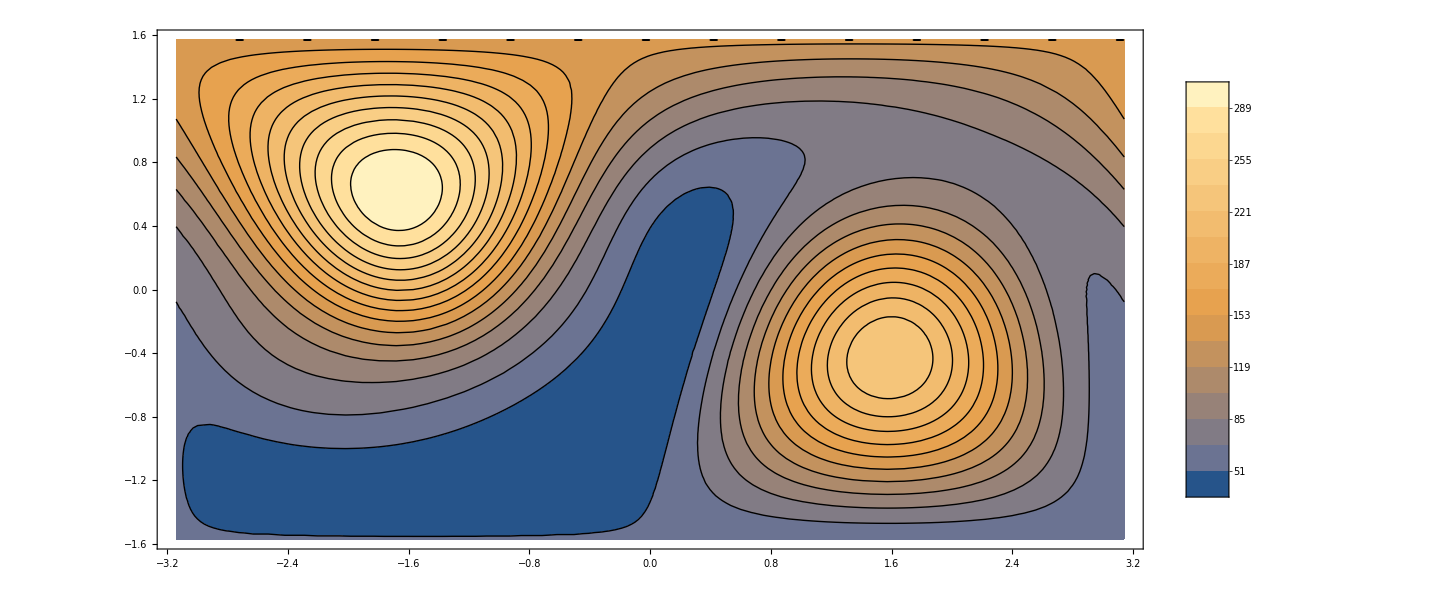

```mathematica
ContourPlot[Sqrt[Bx[er,lat,lon]^2+By[er,lat,lon]^2+Bz[er,lat,lon]^2],{lon,-Pi,Pi},{lat,-Pi/2,Pi/2} ,PlotTheme->"Detailed",Contours->15,AspectRatio->1/2,PlotLegends->Placed[Automatic,After],ImageSize->1200,ContourStyle->Directive[Black,Medium,Opacity[1]]]
```

```mathematica
(*Real magnetic field, in nT*)
```

```mathematica
RBx[lat_,lon_]:=-Sin[lon]*QuantityMagnitude[GeomagneticModelData[GeoPosition[{lat*180/Pi,lon*180/Pi}],"EastComponent"]]-Sin[lat]*Cos[lon]*QuantityMagnitude[GeomagneticModelData[GeoPosition[{lat*180/Pi,lon*180/Pi}],"NorthComponent"]]-Cos[lat]*Cos[lon]*QuantityMagnitude[GeomagneticModelData[GeoPosition[{lat*180/Pi,lon*180/Pi}],"DownComponent"]]
```

```mathematica
RBy[lat_,lon_]:=Cos[lon]*QuantityMagnitude[GeomagneticModelData[GeoPosition[{lat*180/Pi,lon*180/Pi}],"EastComponent"]]-Sin[lat]*Sin[lon]*QuantityMagnitude[GeomagneticModelData[GeoPosition[{lat*180/Pi,lon*180/Pi}],"NorthComponent"]]-Cos[lat]*Sin[lon]*QuantityMagnitude[GeomagneticModelData[GeoPosition[{lat*180/Pi,lon*180/Pi}],"DownComponent"]]
```

```mathematica
RBz[lat_,lon_]:=Cos[lat]*QuantityMagnitude[GeomagneticModelData[GeoPosition[{lat*180/Pi,lon*180/Pi}],"NorthComponent"]]-Sin[lat]*QuantityMagnitude[GeomagneticModelData[GeoPosition[{lat*180/Pi,lon*180/Pi}],"DownComponent"]]
```

```mathematica
(*Plot of (calculated minus real) magnetic field intensity, in μT*)
```

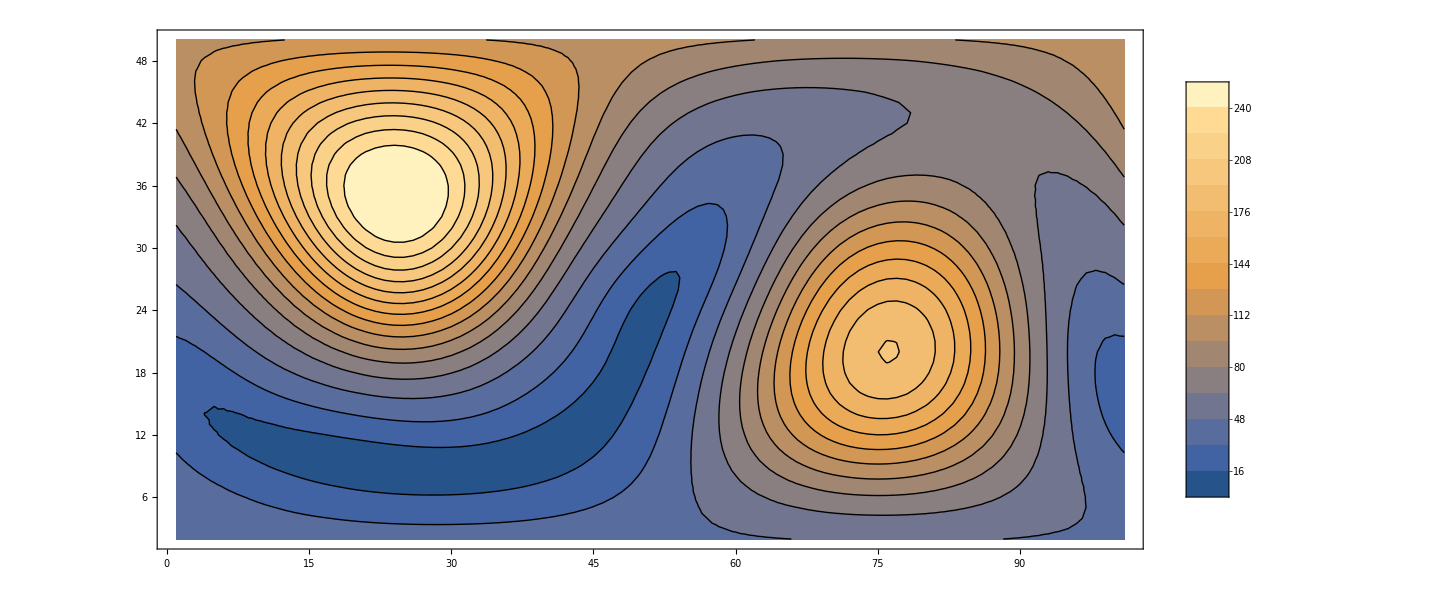

```mathematica
ListContourPlot[Table[Norm[{Bx[er,lat,lon],By[er,lat,lon],Bz[er,lat,lon]}-10^-3*{RBx[lat,lon],RBy[lat,lon],RBz[lat,lon]}],{lat,-Pi/2,Pi/2,Pi/50},{lon,-Pi,Pi,Pi/50}] ,PlotTheme->"Detailed",Contours->15,AspectRatio->1/2,PlotLegends->Placed[Automatic,After],ImageSize->1200,ContourStyle->Directive[Black,Medium,Opacity[1]]]
```

```mathematica
(*Plot of ISS's trajectory*)
```

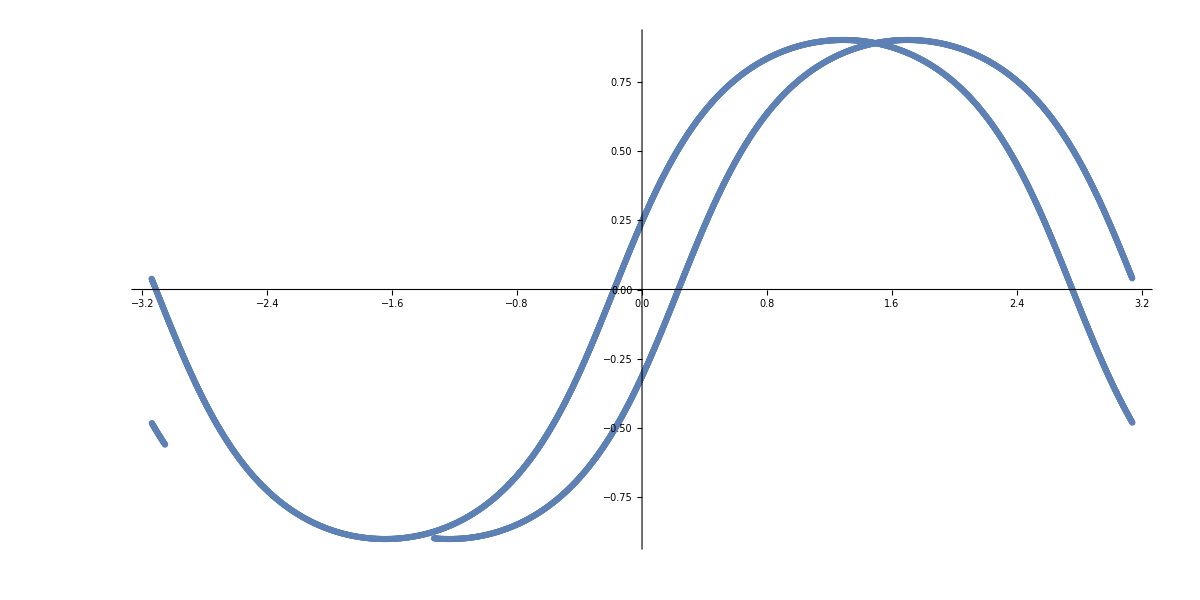

```mathematica
ListPlot[Table[{lon[i],lat[i]},{i,1,4871}],AspectRatio->1/2,ImageSize->1200]
```